```mathematica
170/112. 225
```

341.518

```mathematica
a={{0,1,1,0},{0,0,1,0},{1,0,0,1},{1,0,0,0}}
```

{{0,1,1,0},{0,0,1,0},{1,0,0,1},{1,0,0,0}}

```mathematica
(a9=MatrixPower[a,9])//MatrixForm
```

(28 | 17 | 27 | 17
17 | 11 | 17 | 10
27 | 17 | 28 | 17
17 | 10 | 17 | 11)

```mathematica
{{1,0,1,0}}.a9.Transpose@{{1,1,1,1}}
```

{{178}}

```mathematica
(Drop[#,1]&@(Drop[#,1]&/@CoefficientList[Expand@(Times@@Table[1+x^k y, {k,9}]),{x,y}]))//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 4 | 5 | 1 | 0 | 0 | 0 | 0 | 0
0 | 3 | 7 | 2 | 0 | 0 | 0 | 0 | 0
0 | 3 | 7 | 3 | 0 | 0 | 0 | 0 | 0
0 | 2 | 8 | 5 | 0 | 0 | 0 | 0 | 0
0 | 2 | 8 | 6 | 1 | 0 | 0 | 0 | 0
0 | 1 | 8 | 8 | 1 | 0 | 0 | 0 | 0
0 | 1 | 7 | 9 | 2 | 0 | 0 | 0 | 0
0 | 0 | 7 | 11 | 3 | 0 | 0 | 0 | 0
0 | 0 | 5 | 11 | 5 | 0 | 0 | 0 | 0
0 | 0 | 4 | 12 | 6 | 0 | 0 | 0 | 0
0 | 0 | 3 | 11 | 8 | 1 | 0 | 0 | 0
0 | 0 | 2 | 11 | 9 | 1 | 0 | 0 | 0
0 | 0 | 1 | 9 | 11 | 2 | 0 | 0 | 0
0 | 0 | 1 | 8 | 11 | 3 | 0 | 0 | 0
0 | 0 | 0 | 6 | 12 | 4 | 0 | 0 | 0
0 | 0 | 0 | 5 | 11 | 5 | 0 | 0 | 0
0 | 0 | 0 | 3 | 11 | 7 | 0 | 0 | 0
0 | 0 | 0 | 2 | 9 | 7 | 1 | 0 | 0
0 | 0 | 0 | 1 | 8 | 8 | 1 | 0 | 0
0 | 0 | 0 | 1 | 6 | 8 | 2 | 0 | 0
0 | 0 | 0 | 0 | 5 | 8 | 2 | 0 | 0
0 | 0 | 0 | 0 | 3 | 7 | 3 | 0 | 0
0 | 0 | 0 | 0 | 2 | 7 | 3 | 0 | 0
0 | 0 | 0 | 0 | 1 | 5 | 4 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4 | 4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 2 | 3 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 3 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
maxN=6;
Prepend[#,Table[k,{k,0,maxN}]]&@
(i=1;(Prepend[#,i++]&/@(Drop[#,1]&@(Drop[#,1]&/@CoefficientList[Expand@(Times@@Table[1+x^k y, {k,maxN}]),{x,y}]))))//MatrixForm
```

(0 | 1 | 2 | 3 | 4 | 5 | 6
1 | 1 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0
3 | 1 | 1 | 0 | 0 | 0 | 0
4 | 1 | 1 | 0 | 0 | 0 | 0
5 | 1 | 2 | 0 | 0 | 0 | 0
6 | 1 | 2 | 1 | 0 | 0 | 0
7 | 0 | 3 | 1 | 0 | 0 | 0
8 | 0 | 2 | 2 | 0 | 0 | 0
9 | 0 | 2 | 3 | 0 | 0 | 0
10 | 0 | 1 | 3 | 1 | 0 | 0
11 | 0 | 1 | 3 | 1 | 0 | 0
12 | 0 | 0 | 3 | 2 | 0 | 0
13 | 0 | 0 | 2 | 2 | 0 | 0
14 | 0 | 0 | 1 | 3 | 0 | 0
15 | 0 | 0 | 1 | 2 | 1 | 0
16 | 0 | 0 | 0 | 2 | 1 | 0
17 | 0 | 0 | 0 | 1 | 1 | 0
18 | 0 | 0 | 0 | 1 | 1 | 0
19 | 0 | 0 | 0 | 0 | 1 | 0
20 | 0 | 0 | 0 | 0 | 1 | 0
21 | 0 | 0 | 0 | 0 | 0 | 1)

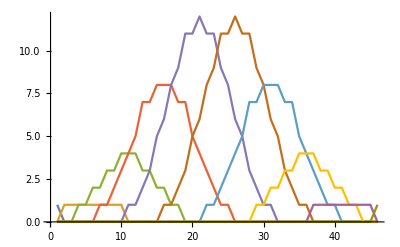

```mathematica
maxN=9;
CoefficientList[Expand@(Times@@Table[1+x^k y, {k,maxN}]),{x,y}]//Transpose//ListLinePlot[#,PlotRange->All]&
```

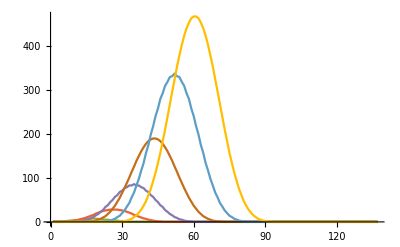

```mathematica
maxN=16;
CoefficientList[Expand@(Times@@Table[1+x^k y, {k,maxN}]),{x,y}]//Transpose//Take[#,Round[Length[#]/2]]&//ListLinePlot[#,PlotRange->All]&
```

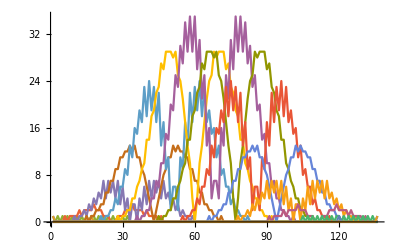

```mathematica
maxN=16;
((CoefficientList[Expand@(Times@@Table[1+x^k y, {k,maxN}]),{x,y}]//Transpose))//
Table[Abs[#[[i]]-#[[i+1]]],{i,Length[#]-1}]&/@#&//


ListLinePlot[#,PlotRange->All]&
```